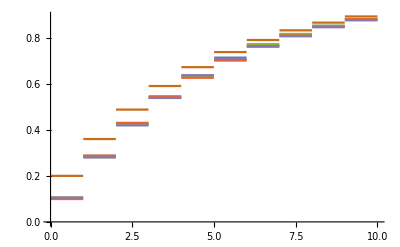

```mathematica
a1 = ReadList["C:\\Users\\MI\\Documents\\GitHub\\Math-Stat\\Geom\\Geom10000_1.txt", Number];
a2 = ReadList["C:\\Users\\MI\\Documents\\GitHub\\Math-Stat\\Geom\\Geom10000_2.txt", Number];
a3 = ReadList["C:\\Users\\MI\\Documents\\GitHub\\Math-Stat\\Geom\\Geom10000_3.txt", Number];
a4 = ReadList["C:\\Users\\MI\\Documents\\GitHub\\Math-Stat\\Geom\\Geom10000_4.txt", Number];
a5 = ReadList["C:\\Users\\MI\\Documents\\GitHub\\Math-Stat\\Geom\\Geom10000_5.txt", Number];
c1 = EmpiricalDistribution[a1];
c2 = EmpiricalDistribution[a2];
c3 = EmpiricalDistribution[a3];
c4 = EmpiricalDistribution[a4];
c5 = EmpiricalDistribution[a5];
Plot[{CDF[c1,x],CDF[c2,x],CDF[c3,x],CDF[c4,x],CDF[c5,x], CDF[GeometricDistribution[0.2],x]},{x,0,10}]
```